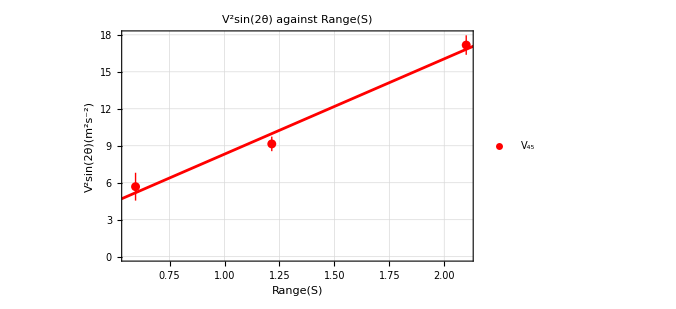
-Graphics-
V_45: y==7.73209 x+0.589179

```mathematica
(*Define the data*)V45={{0.595,5.68},{1.215,9.15},{2.1,17.17}};

(*error bar*)
V45error={{Around[0.595,0.001],Around[5.68,1.13]},{Around[1.215,0.001],Around[9.15,0.59]},{Around[2.1,0.001],Around[17.17,0.79]}};

(*Extract x and y values for each set of data*)
x1=V45[[All,1]];
y1=V45[[All,2]];

(*Perform linear regression to find the best-fit lines*)
fit1=LinearModelFit[V45,x,x];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fit1["BestFit"]]];

(*Display the equations outside the graph with extended line plot*)
Column[{Show[ListPlot[{V45error},PlotStyle->{Red},PlotLegends->{"\!\(\*SubscriptBox[\(V\), \(45\)]\)"}],Plot[{fit1[x]},{x,0,2.5},PlotStyle->{Red},PlotRange->{{0,2.5},Automatic}],Frame->True,FrameLabel->{"Range(S)","\!\(\*SuperscriptBox[\(V\), \(2\)]\)sin(2θ)(m^2s^-2)"},GridLines->Automatic,PlotLabel->"\!\(\*SuperscriptBox[\(V\), \(2\)]\)sin(2θ) against Range(S) ",ImageSize->500],Column[{Row[{"\!\(\*SubscriptBox[\(V\), \(45\)]\): ",eq1}]}]}]
```